# Les polynômes de Legendre en coordonnées polaires

## Définition du produit scalaire

### Fonction poid

```mathematica
w:=Sin[θ]
```

### Intervalle d’orthogonalité

```mathematica
a:=0
```

```mathematica
b:=π
```

### Produit scalaire

```mathematica
⟨f_|g_⟩:=∫_a^b w f gⅆθ
```

## Norme et normalization

### Norme

```mathematica
norm[x_]:=√⟨x|x⟩
```

### Normalization

```mathematica
normalize[x_]:=x/(√⟨x|x⟩)
```

### Normalization d’un ensemble

```mathematica
normalizeListe[vectors_]:=Table[normalize[vectors[[i]]],{i,1,Length[vectors]}]
```

## Projection orthogonale

```mathematica
projection[y_,x_]:=⟨x|y⟩x/⟨x|x⟩
```

## Orthogonalisation (Procédé de Gram-Schmidt)

```mathematica
gramSchmidt[vectors_]:=Module[{oVectors=vectors},
Do[oVectors[[i]]-=projection[oVectors[[i]],oVectors[[j]]],{i,2,Length[vectors]},{j,1,i-1}];
oVectors]
```

### Matrice d’orthonormalité

```mathematica
orthogonality[vectors_]:=Table[⟨vectors[[i]]|vectors[[j]]⟩,{i,1,Length[vectors]},{j,1,Length[vectors]}]//Simplify//TableForm
```

## Base

### Base orthogonale

```mathematica
dim:=5
```

```mathematica
Subscript[n, min]:=0;Subscript[n, max]:=dim-1;
```

```mathematica
Subscript[𝓊, n_][θ_]:=LegendreP[n,Cos[θ]]
```

```mathematica
Table[Subscript[𝓊, n][θ],{n,Subscript[n, min],Subscript[n, max]}]//TableForm//TraditionalForm
```

1
cos(θ)
1/2 (3 cos^2(θ)-1)
1/2 (5 cos^3(θ)-3 cos(θ))
1/8 (35 cos^4(θ)-30 cos^2(θ)+3)

```mathematica
orthogonality[Table[Subscript[𝓊, n][θ],{n,Subscript[n, min],Subscript[n, max]}]]
```

2 | 0 | 0 | 0 | 0
0 | 2/3 | 0 | 0 | 0
0 | 0 | 2/5 | 0 | 0
0 | 0 | 0 | 2/7 | 0
0 | 0 | 0 | 0 | 2/9

### Représentation graphique

```mathematica
Subscript[θ, min]:=0;Subscript[θ, max]:=2π;
```

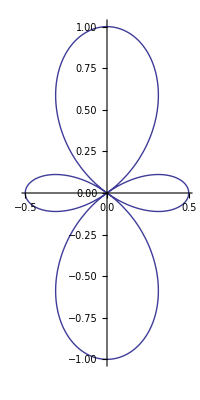

```mathematica
ParametricPlot[{Sin[θ],Cos[θ]}Subscript[𝓊, 2][θ],{θ,Subscript[θ, min],Subscript[θ, max]}]
```

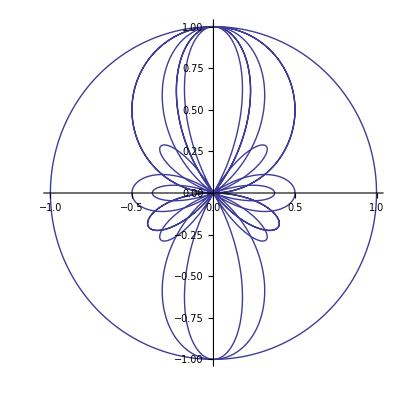

```mathematica
ParametricPlot[Table[{Sin[θ],Cos[θ]}Subscript[𝓊, n][θ] ,{n,Subscript[n, min],Subscript[n, max]}],{θ,Subscript[θ, min],Subscript[θ, max]}]
```

### Base orthonormale

On peut normaliser cette base

```mathematica
Subscript[𝓊̃, n_][θ_]:=normalize[Subscript[𝓊, n][θ]]
```

```mathematica
Table[Subscript[𝓊̃, n][θ],{n,Subscript[n, min],Subscript[n, max]}]//Simplify//TableForm//TraditionalForm
```

1/(√2)
√(3/2) cos(θ)
1/4 √(5/2) (3 cos(2 θ)+1)
1/8 √(7/2) (3 cos(θ)+5 cos(3 θ))
(3 (20 cos(2 θ)+35 cos(4 θ)+9))/(64 √2)

```mathematica
orthogonality[Table[Subscript[𝓊̃, n][θ],{n,Subscript[n, min],Subscript[n, max]}]]
```

1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1

### Représentation graphique

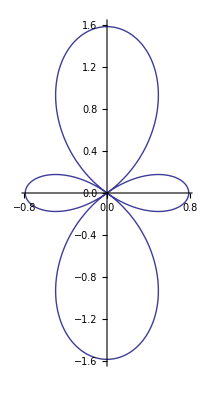

```mathematica
ParametricPlot[Evaluate[{Sin[θ],Cos[θ]}Subscript[𝓊̃, 2][θ]],{θ,Subscript[θ, min],Subscript[θ, max]}]
```

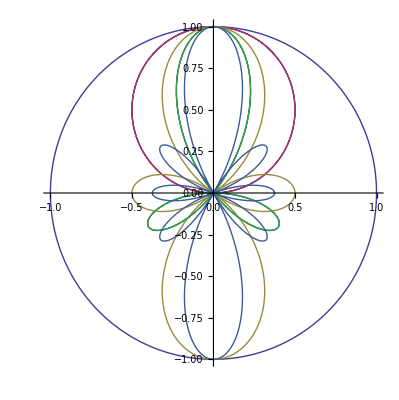

```mathematica
ParametricPlot[Evaluate[Table[{Sin[θ],Cos[θ]}Subscript[𝓊, n][θ] ,{n,Subscript[n, min],Subscript[n, max]}]],{θ,Subscript[θ, min],Subscript[θ, max]}]
```

## Développement

### La fonction à développer

```mathematica
f[θ_] :=Sin[θ/2]
```

### Les coeficients de Fourier

```mathematica
Subscript[a, n_]:=⟨Subscript[𝓊̃, n][θ]|f[θ] ⟩
```

```mathematica
Table[Subscript[a, n],{n,Subscript[n, min],Subscript[n, max]}]//Simplify
```

{(2 √2)/3,-(2 √(2/3))/5,-(2 √(2/5))/21,-(2 √(2/7))/45,-(2 √2)/231}

### Dévelopement de f(x) sur la base orthonormale

```mathematica
∑_(n=0)^10 Subscript[a, n] Subscript[𝓊̃, n]
```

2/3 √2 (𝓊̃)_0-2/5 √(2/3) (𝓊̃)_1-2/21 √(2/5) (𝓊̃)_2-2/45 √(2/7) (𝓊̃)_3-2/231 √2 (𝓊̃)_4-2/117 √(2/11) (𝓊̃)_5-2/165 √(2/13) (𝓊̃)_6-2/221 √(2/15) (𝓊̃)_7-2/285 √(2/17) (𝓊̃)_8-2/357 √(2/19) (𝓊̃)_9-2/437 √(2/21) (𝓊̃)_10

```mathematica
Manipulate[∑_(n=0)^N Subscript[a, n] Subscript[𝓊̃, n][θ],{N,0,10,1}]
```

```mathematica
Manipulate[Plot[Evaluate[{f[θ],∑_(n=0)^N Subscript[a, n] Subscript[𝓊̃, n][θ]}],{θ,Subscript[θ, min],Subscript[θ, max]},PlotRange->All],{N,0,10,1},ControlType->Setter]
```